# Heat Conduction; numerical solution of steady state problem

## ENGENER201 - Transport Phenomena

Friso Meeusen
May 12, 2022

```mathematica
(* This clears all variables and definitions: *)
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
(* This defines the number of internal celss: *)
n=20;
```

```mathematica
(* This defines the initial temperature field: *)
Told=Table[0,{n+2},{n+2}];
(* This defines the boundary conditions: *)
Told[[All,1]]=0;
Told[[1,All]]=0;
Told[[All,-1]]=50;
Told[[-1,All]]=50;
ArrayPlot[Told,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, PlotLegends->Automatic]
```

```mathematica
(* This shows the inital temperature field *)
```

-Graphics-

```mathematica
(* This initializes new field: *)
Tnew=Told;
```

```mathematica
(* This initializes convergence parameter: *)
ϵ=1;
(* This sets the convergence criterion: *)
ϵconv=10^-3;
```

```mathematica
(* This calculates new temperature profile: *)
Monitor[
While[ϵ>ϵconv,
Do[
(*Here Tnew[[ii,jj]]corresponds to Tp (as it is called in the paper). 
Told[[ii-1,jj]] corresponds with Tw, 
  Told[[ii+1,jj]] corresponds with Te, 
  Told[[ii,jj-1]] corresponds with Tn 
 and Told[[ii,jj+1]] corresponds with Ts*)
(*Tp is calculated using the formula of the Picard iteration *)
Tnew[[ii,jj]]=1/4(Told[[ii-1,jj]]+Told[[ii+1,jj]]+Told[[ii,jj-1]]+Told[[ii,jj+1]]);
,{ii,2,n+1},{jj,2,n+1}];
(* This calculates the new convergence: *)
ϵ=Total[Abs[Tnew-Told],2];
(* This replaces the old field with the new field: *)
Told=Tnew;
];
,ProgressIndicator[Dynamic[1/ϵ],{0,1/ϵconv}]]
```

```mathematica
(* This generates an arrayplot of the steady state temperature field: *)
(* The origin in an arrayplot is top left! *)
ArrayPlot[Told,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic, PlotLegends->Automatic]
```

-Graphics-

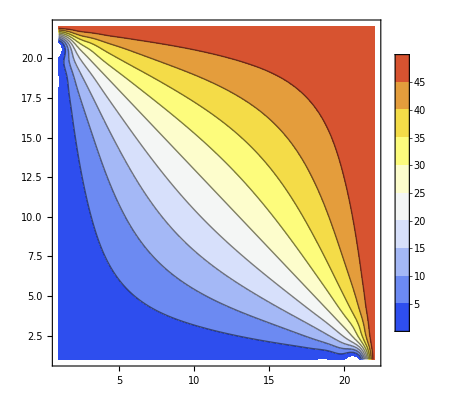

```mathematica
(* This generates a contourplot of the temperature field: *)
(* The origin in a list contourplot is bottom left! *)
ListContourPlot[Tnew,InterpolationOrder->3,PlotLegends->Automatic,ColorFunction->"TemperatureMap"]
```

## Heat Production Involved

```mathematica
(* we can now also consider a different heat balance: one where there is also a heat production, q involved (see TP pp. 135-136).
```

```mathematica
(* This defines the temperature field (same as in the section above): *)
```

```mathematica
Toldq=Table[0,{n+2},{n+2}];
(* This defines the boundary conditions: *)
(* Unlike the section above (where no production was involed) all boundary conditions are now 0°C for each side *)
Toldq[[All,1]]=0;
Toldq[[1,All]]=0;
Toldq[[All,-1]]=0;
Toldq[[-1,All]]=0;
ArrayPlot[Toldq,ColorFunction->"TemperatureMap",Axes->True,FrameTicks->Automatic,PlotLegends->Automatic]
```

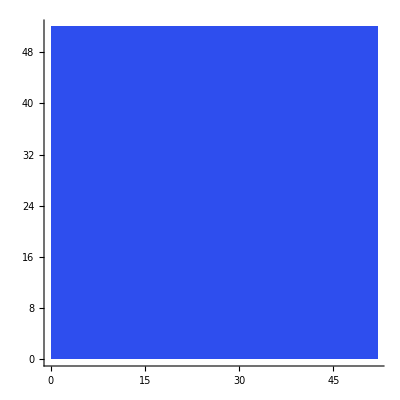

```mathematica
(* This shows the inital Temperature field *)
```

```mathematica
(* This defines the heat production field q *)
```

```mathematica
q=Table[0,{n+2},{n+2}];
```

```mathematica
(* This defines the location and value of the source of the heat production (q=100 W/m^2) and sink (q=-100 W/m^2). All other cells have a production value of q=0 ;*)
```

```mathematica
q[[All,All]]=0;
```

```mathematica
(* The source is set at (5,15) and the sink is set at (15,5) *)
```

```mathematica
q[[5,15]]=100;
q[[15,5]]=-100;
ArrayPlot[q,ColorFunction->"TemperatureMap",Axes->True,PlotLegends->Automatic]
```

```mathematica
(* This shows the heat production field q*)
```

-Graphics-

```mathematica
(* This initializes new field: *)
Tnewq=Toldq;
```

```mathematica
(* We use the same value for the convergion paramter (ϵ = 1) and convergion cirteria (ϵconv = 10^-3) as above *)
```

```mathematica
(* According to Fourier's law,we need to have a value for the thermal conductivity coefficient. In this example I will use the value for copper (λ=401 W/(m*K)) *)
λ=401;
```

```mathematica
(* This initializes convergence parameter: *)
ϵ=1;
(* This sets the convergence criterion: *)
ϵconv=10^-3;
```

```mathematica
(* This calculates new temperature profile: *)
Monitor[
While[ϵ>ϵconv,
Do[
(* The formula of the Picard iteration now also contains a heat production term*)
Tnewq[[ii,jj]]=1/4(Toldq[[ii-1,jj]]+Toldq[[ii+1,jj]]+Toldq[[ii,jj-1]]+Toldq[[ii,jj+1]])+1/(4*λ)*q[[ii,jj]];
,{ii,2,n+1},{jj,2,n+1}];
(* This calculates the new convergence: *)
ϵ=Total[Abs[Tnewq-Toldq],2];
(* This replaces the old field with the new field: *)
Toldq=Tnewq;
];
,ProgressIndicator[Dynamic[1/ϵ],{0,1/ϵconv}]]
```

```mathematica
ArrayPlot[Toldq,ColorFunction->"TemperatureMap",Axes->True,PlotLegends -> Automatic, FrameTicks->Automatic]
```

```mathematica
(* This shows the resultin steady state temperature field*)
```

-Graphics-